```mathematica
f[x_,y_]= Exp[x+y]
```

ⅇ^(x+y)

```mathematica
phiTri[a_,b_,c_,{x_,y_}]:=Module[{p,α,β},
{α,β}=LinearSolve[{{Norm[b-a]^2,(b-a).(c-a)},{(b-a).(c-a),Norm[c-a]^2}},{-1,-1}];
p = α (b-a) + β (c-a);
Return[1 + p.({x,y}-a)]
]
```

```mathematica
phiRef[x_,y_]={1-x-y,x,y}
```

{-x-y+1,x,y}

```mathematica
phiProdRef[x_,y_]=KroneckerProduct[phiRef[x,y],phiRef[x,y]]
```

((-x-y+1)^2 | x (-x-y+1) | y (-x-y+1)
x (-x-y+1) | x^2 | x y
y (-x-y+1) | x y | y^2)

```mathematica
{aa, bb, cc}={{-1/4,1/8},{5/4,0},{1,4/3}}
```

(-1/4 | 1/8
5/4 | 0
1 | 4/3)

```mathematica
phiPhys[x_,y_]={phiTri[aa,bb,cc,{x,y}],phiTri[bb,cc,aa,{x,y}],phiTri[cc,aa,bb,{x,y}]}
```

{-128/189 (x+1/4)-8/63 (y-1/8)+1,116/189 (x-5/4)-(40 y)/63+1,(4 (x-1))/63+16/21 (y-4/3)+1}

```mathematica
phiProdPhys[x_,y_]=KroneckerProduct[phiPhys[x,y],phiPhys[x,y]]
```

((-128/189 (x+1/4)-8/63 (y-1/8)+1)^2 | (-128/189 (x+1/4)-8/63 (y-1/8)+1) (116/189 (x-5/4)-(40 y)/63+1) | ((4 (x-1))/63+16/21 (y-4/3)+1) (-128/189 (x+1/4)-8/63 (y-1/8)+1)
(-128/189 (x+1/4)-8/63 (y-1/8)+1) (116/189 (x-5/4)-(40 y)/63+1) | (116/189 (x-5/4)-(40 y)/63+1)^2 | ((4 (x-1))/63+16/21 (y-4/3)+1) (116/189 (x-5/4)-(40 y)/63+1)
((4 (x-1))/63+16/21 (y-4/3)+1) (-128/189 (x+1/4)-8/63 (y-1/8)+1) | ((4 (x-1))/63+16/21 (y-4/3)+1) (116/189 (x-5/4)-(40 y)/63+1) | ((4 (x-1))/63+16/21 (y-4/3)+1)^2)

```mathematica
{phiPhys[aa[[1]],aa[[2]]], phiPhys[bb[[1]],bb[[2]]],phiPhys[cc[[1]],cc[[2]]]}
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
R = Triangle[{{0,0},{1,0},{0,1}}]
```

Triangle[(0 | 0
1 | 0
0 | 1)]

```mathematica
T = Triangle[{aa,bb,cc}]
```

Triangle[(-1/4 | 1/8
5/4 | 0
1 | 4/3)]

```mathematica
fileNum = "9"
```

9

```mathematica
refQP = Import["/Users/katharine/Projects/PyPDE/DemoFE/Quadrature/strang"<>fileNum <> "_x.txt", "Table"]
```

(0.873822 | 0.063089
0.063089 | 0.873822
0.063089 | 0.063089
0.501427 | 0.249287
0.249287 | 0.501427
0.249287 | 0.249287
0.636502 | 0.310352
0.636502 | 0.053145
0.310352 | 0.636502
0.310352 | 0.053145
0.053145 | 0.636502
0.053145 | 0.310352)

```mathematica
physQP = Table[aa + (bb -aa)p[[1]] + (cc-aa)p[[2]],{p,refQP}]
```

(1.13959 | 0.0920048
0.936911 | 1.17298
-0.0765052 | 0.193346
0.813748 | 0.363543
0.750713 | 0.69973
0.435539 | 0.395061
1.09269 | 0.420446
0.771185 | 0.109654
1.01116 | 0.855313
0.28196 | 0.150423
0.625346 | 0.887464
0.217658 | 0.493366)

```mathematica
w = Flatten[Import["/Users/katharine/Projects/PyPDE/DemoFE/Quadrature/strang"<> fileNum <>"_w.txt", "Table"]]
```

{0.0508449,0.0508449,0.0508449,0.116786,0.116786,0.116786,0.0828511,0.0828511,0.0828511,0.0828511,0.0828511,0.0828511}

```mathematica
phiProdAtRefQP = Table[phiProdRef[refQP[[i,1]],refQP[[i,2]]],{i,1,Length[w]}]
```

({0.00398022,0.0551286,0.00398022} | {0.0551286,0.763565,0.0551286} | {0.00398022,0.0551286,0.00398022}
{0.00398022,0.00398022,0.0551286} | {0.00398022,0.00398022,0.0551286} | {0.0551286,0.0551286,0.763565}
{0.763565,0.0551286,0.0551286} | {0.0551286,0.00398022,0.00398022} | {0.0551286,0.00398022,0.00398022}
{0.0621439,0.124999,0.0621439} | {0.124999,0.251429,0.124999} | {0.0621439,0.124999,0.0621439}
{0.0621439,0.0621439,0.124999} | {0.0621439,0.0621439,0.124999} | {0.124999,0.124999,0.251429}
{0.251429,0.124999,0.124999} | {0.124999,0.0621439,0.0621439} | {0.124999,0.0621439,0.0621439}
{0.0028244,0.033827,0.0164937} | {0.033827,0.405135,0.19754} | {0.0164937,0.19754,0.0963186}
{0.0963186,0.19754,0.0164937} | {0.19754,0.405135,0.033827} | {0.0164937,0.033827,0.0028244}
{0.0028244,0.0164937,0.033827} | {0.0164937,0.0963186,0.19754} | {0.033827,0.19754,0.405135}
{0.405135,0.19754,0.033827} | {0.19754,0.0963186,0.0164937} | {0.033827,0.0164937,0.0028244}
{0.0963186,0.0164937,0.19754} | {0.0164937,0.0028244,0.033827} | {0.19754,0.033827,0.405135}
{0.405135,0.033827,0.19754} | {0.033827,0.0028244,0.0164937} | {0.19754,0.0164937,0.0963186})

```mathematica
phiProdAtPhysQP =  Table[phiProdPhys[physQP[[i,1]],physQP[[i,2]]],{i,1,Length[w]}]
```

({0.00398022,0.0551286,0.00398022} | {0.0551286,0.763565,0.0551286} | {0.00398022,0.0551286,0.00398022}
{0.00398022,0.00398022,0.0551286} | {0.00398022,0.00398022,0.0551286} | {0.0551286,0.0551286,0.763565}
{0.763565,0.0551286,0.0551286} | {0.0551286,0.00398022,0.00398022} | {0.0551286,0.00398022,0.00398022}
{0.0621439,0.124999,0.0621439} | {0.124999,0.251429,0.124999} | {0.0621439,0.124999,0.0621439}
{0.0621439,0.0621439,0.124999} | {0.0621439,0.0621439,0.124999} | {0.124999,0.124999,0.251429}
{0.251429,0.124999,0.124999} | {0.124999,0.0621439,0.0621439} | {0.124999,0.0621439,0.0621439}
{0.0028244,0.033827,0.0164937} | {0.033827,0.405135,0.19754} | {0.0164937,0.19754,0.0963186}
{0.0963186,0.19754,0.0164937} | {0.19754,0.405135,0.033827} | {0.0164937,0.033827,0.0028244}
{0.0028244,0.0164937,0.033827} | {0.0164937,0.0963186,0.19754} | {0.033827,0.19754,0.405135}
{0.405135,0.19754,0.033827} | {0.19754,0.0963186,0.0164937} | {0.033827,0.0164937,0.0028244}
{0.0963186,0.0164937,0.19754} | {0.0164937,0.0028244,0.033827} | {0.19754,0.033827,0.405135}
{0.405135,0.033827,0.19754} | {0.033827,0.0028244,0.0164937} | {0.19754,0.0164937,0.0963186})

```mathematica
Qex=Integrate[f[x,y]phiProdPhys[x,y], {x, y}∈ T]//N
```

(0.340607 | 0.220928 | 0.281364
0.220928 | 0.567675 | 0.358072
0.281364 | 0.358072 | 0.89515)

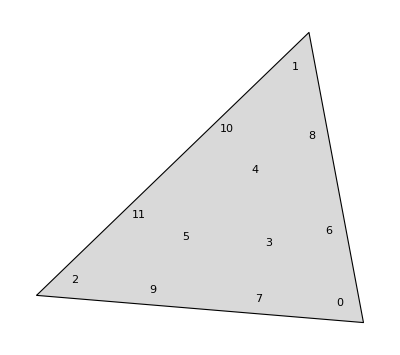

```mathematica
Graphics[{FaceForm[LightGray],EdgeForm[Black],T,Table[Text[i-1,physQP[[i]]],{i,1,Length[physQP]}]}]
```

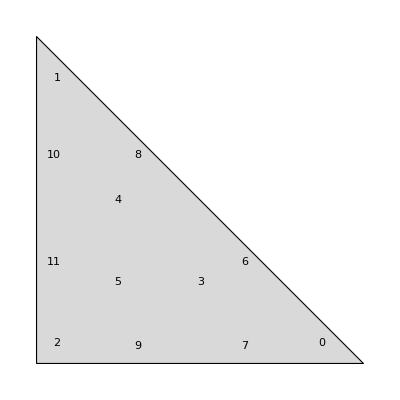

```mathematica
Graphics[{FaceForm[LightGray],EdgeForm[Black],R,Table[Text[i-1,refQP[[i]]],{i,1,Length[refQP]}]}]
```

```mathematica
fVals = f[physQP[[;;,1]],physQP[[;;,2]]]
```

{3.4267,8.24736,1.12394,3.24557,4.265,2.29469,4.54097,2.41292,6.46543,1.54092,4.53947,2.03608}

```mathematica
wf = w fVals
```

{0.17423,0.419336,0.0571467,0.379038,0.498094,0.267989,0.376224,0.199913,0.535668,0.127667,0.3761,0.168691}

```mathematica
phiProdAtRefQP[[1]]
```

(0.00398022 | 0.0551286 | 0.00398022
0.0551286 | 0.763565 | 0.0551286
0.00398022 | 0.0551286 | 0.00398022)

```mathematica
wfTimesPhiProdAtRefQP = Table[wf[[i]]phiProdAtRefQP[[i]],{i,1,Length[w]}]
```

({0.000693476,0.00960508,0.000693476} | {0.00960508,0.133036,0.00960508} | {0.000693476,0.00960508,0.000693476}
{0.00166905,0.00166905,0.0231174} | {0.00166905,0.00166905,0.0231174} | {0.0231174,0.0231174,0.32019}
{0.0436352,0.00315041,0.00315041} | {0.00315041,0.000227457,0.000227457} | {0.00315041,0.000227457,0.000227457}
{0.0235549,0.0473794,0.0235549} | {0.0473794,0.095301,0.0473794} | {0.0235549,0.0473794,0.0235549}
{0.0309535,0.0309535,0.0622612} | {0.0309535,0.0309535,0.0622612} | {0.0622612,0.0622612,0.125235}
{0.06738,0.0334983,0.0334983} | {0.0334983,0.0166539,0.0166539} | {0.0334983,0.0166539,0.0166539}
{0.00106261,0.0127265,0.00620533} | {0.0127265,0.152422,0.0743194} | {0.00620533,0.0743194,0.0362374}
{0.0192554,0.0394909,0.00329731} | {0.0394909,0.080992,0.00676246} | {0.00329731,0.00676246,0.000564634}
{0.00151294,0.00883515,0.01812} | {0.00883515,0.0515948,0.105816} | {0.01812,0.105816,0.217018}
{0.0517225,0.0252194,0.0043186} | {0.0252194,0.0122967,0.00210571} | {0.0043186,0.00210571,0.000360583}
{0.0362254,0.00620328,0.0742948} | {0.00620328,0.00106225,0.0127223} | {0.0742948,0.0127223,0.152371}
{0.0683427,0.0057063,0.0333232} | {0.0057063,0.00047645,0.00278234} | {0.0333232,0.00278234,0.0162481})

```mathematica
wfTimesPhiProdAtPhysQP = Table[wf[[i]]phiProdAtPhysQP[[i]],{i,1,Length[w]}]
```

({0.000693476,0.00960508,0.000693476} | {0.00960508,0.133036,0.00960508} | {0.000693476,0.00960508,0.000693476}
{0.00166905,0.00166905,0.0231174} | {0.00166905,0.00166905,0.0231174} | {0.0231174,0.0231174,0.32019}
{0.0436352,0.00315041,0.00315041} | {0.00315041,0.000227457,0.000227457} | {0.00315041,0.000227457,0.000227457}
{0.0235549,0.0473794,0.0235549} | {0.0473794,0.095301,0.0473794} | {0.0235549,0.0473794,0.0235549}
{0.0309535,0.0309535,0.0622612} | {0.0309535,0.0309535,0.0622612} | {0.0622612,0.0622612,0.125235}
{0.06738,0.0334983,0.0334983} | {0.0334983,0.0166539,0.0166539} | {0.0334983,0.0166539,0.0166539}
{0.00106261,0.0127265,0.00620533} | {0.0127265,0.152422,0.0743194} | {0.00620533,0.0743194,0.0362374}
{0.0192554,0.0394909,0.00329731} | {0.0394909,0.080992,0.00676246} | {0.00329731,0.00676246,0.000564634}
{0.00151294,0.00883515,0.01812} | {0.00883515,0.0515948,0.105816} | {0.01812,0.105816,0.217018}
{0.0517225,0.0252194,0.0043186} | {0.0252194,0.0122967,0.00210571} | {0.0043186,0.00210571,0.000360583}
{0.0362254,0.00620328,0.0742948} | {0.00620328,0.00106225,0.0127223} | {0.0742948,0.0127223,0.152371}
{0.0683427,0.0057063,0.0333232} | {0.0057063,0.00047645,0.00278234} | {0.0333232,0.00278234,0.0162481})

```mathematica
Qref = Total[wfTimesPhiProdAtRefQP]Area[T]
```

(0.340601 | 0.22093 | 0.281369
0.22093 | 0.567674 | 0.358069
0.281369 | 0.358069 | 0.895147)

```mathematica
Qphys =Total[wfTimesPhiProdAtPhysQP] Area[T]
```

(0.340601 | 0.22093 | 0.281369
0.22093 | 0.567674 | 0.358069
0.281369 | 0.358069 | 0.895147)

```mathematica
Qex
```

(0.340607 | 0.220928 | 0.281364
0.220928 | 0.567675 | 0.358072
0.281364 | 0.358072 | 0.89515)